# Homework 19

## Problem 19.1

This is a continuation of written problem #1, so please do that one first.

```mathematica
Quit[]
Clear["'*"]
```

Write down the equations of motion derived in the written problem for x[t] and phi[t].

```mathematica
eqx=x''[t]+((m*l)/(M+m))*(phi''[t]*Cos[phi[t]]-(phi'[t])^2*Sin[phi[t]])+((k*x[t])/(M+m))==0
eqphi=(g/l)*Sin[phi[t]]+(x''[t]/l)*Cos[phi[t]]+phi''[t]==0
```

(k x[t])/(m+M)+(l m (-Sin[phi[t]] phi'[t]^2+Cos[phi[t]] phi''[t]))/(m+M)+x''[t]==0

(g Sin[phi[t]])/l+phi''[t]+(Cos[phi[t]] x''[t])/l==0

### Solutions

x''[t]==-(k x[t]-l m Sin[phi[t]] phi'[t]^2+l m Cos[phi[t]] phi''[t])/(m+M)
phi''[t]==-(g Sin[phi[t]]+Cos[phi[t]] x''[t])/l

Now try various parameter values and initial conditions.

First, let k=0, m=0.5, M=1.0, l=0.25, x[0]=0, x’[0]=0, phi[0]=Pi/6, phi’[0]=0. Do the plots agree with your prediction in written problem 1(b)?

{{x→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

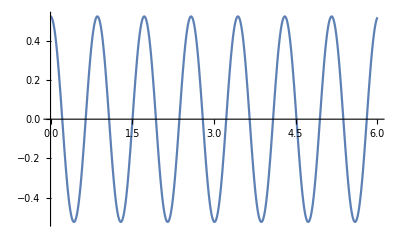

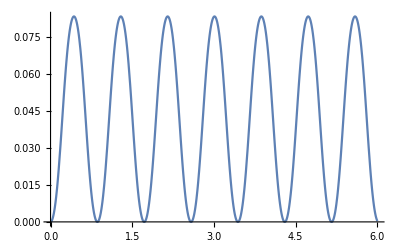

```mathematica
values={k->0,m->0.5,M->1.0,g->9.8,l->0.25};
bc={x[0]==0,x'[0]==0,phi[0]==Pi/6,phi'[0]==0};

sol=NDSolve[{eqx,eqphi,bc}/.values,{x,phi},{t,0,6}]
Plot[Evaluate[phi[t]/.sol],{t,0,6}]
Plot[Evaluate[x[t]/.sol],{t,0,6}]
```

Now use the same values and initial conditions as before but let k=12 N/m.

{{x→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

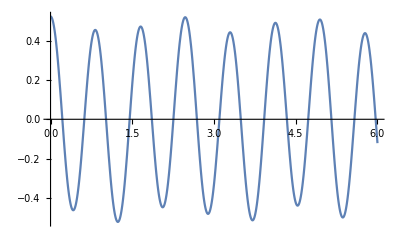

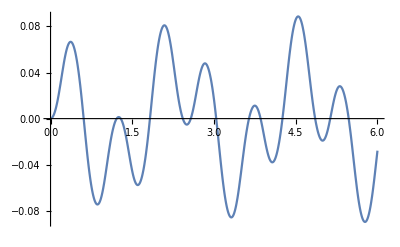

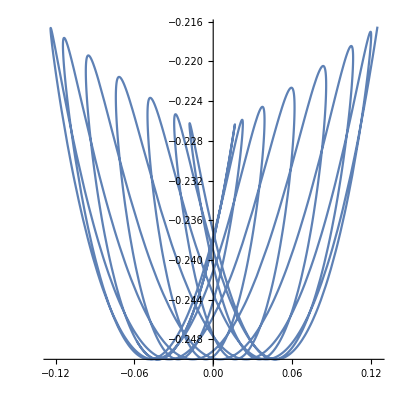

```mathematica
values={k->12,m->0.5,M->1.0,g->9.8,l->0.25};
bc={x[0]==0,x'[0]==0,phi[0]==Pi/6,phi'[0]==0};

sol=NDSolve[{eqx,eqphi,bc}/.values,{x,phi},{t,0,6}]
Plot[Evaluate[phi[t]/.sol],{t,0,6}]
Plot[Evaluate[x[t]/.sol],{t,0,6}]

(* Plot the position of the pendulum bob *)
xpen=(x[t]+l*Sin[phi[t]])/.values;
ypen=(-l*Cos[phi[t]])/.values;
ParametricPlot[Evaluate[{xpen,ypen}/.sol],{t,0,6},AspectRatio->1]
```

With k=12 N/m, give the spring an initial displacement of 15 cm, let the pendulum hang vertically downward initially, and release the system from rest.

{{x→InterpolatingFunction[…],phi→InterpolatingFunction[…]}}

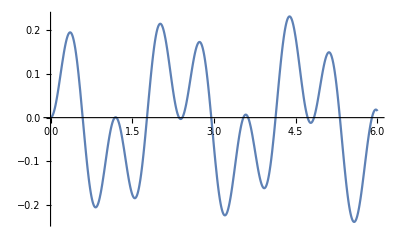

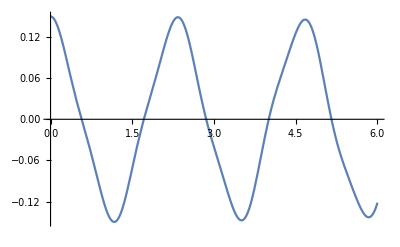

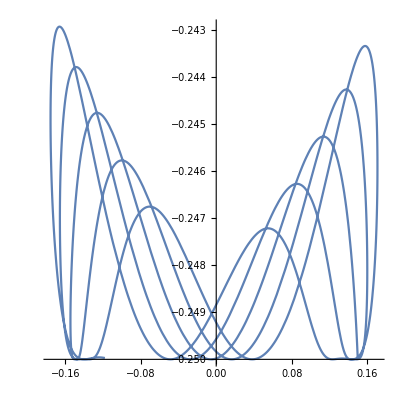

```mathematica
values={k->12,m->0.5,M->1.0,g->9.8,l->0.25};
bc={x[0]==.15,x'[0]==0,phi[0]==0,phi'[0]==0};

sol=NDSolve[{eqx,eqphi,bc}/.values,{x,phi},{t,0,6}]
Plot[Evaluate[phi[t]/.sol],{t,0,6}]
Plot[Evaluate[x[t]/.sol],{t,0,6}]

xpen=(x[t]+l*Sin[phi[t]])/.values;
ypen=(-l*Cos[phi[t]])/.values;
ParametricPlot[Evaluate[{xpen,ypen}/.sol],{t,0,6},AspectRatio->1]
```

## Written Problems

-Graphics-

```mathematica
Quit[]
```

```mathematica
F=m((l^2)/(m^2*r^3))-m*g==2*m*phi*(l/(m*r^2))
```

-g m+l^2/(m r^3)==(2 l phi)/r^2

```mathematica
Solve[F,r]
```

{{r→(2 (2/3)^(1/3) l m phi)/((-9 g^2 l^2 m^4+√3 √(27 g^4 l^4 m^8+32 g^3 l^3 m^9 phi^3))^(1/3))-((-9 g^2 l^2 m^4+√3 √(27 g^4 l^4 m^8+32 g^3 l^3 m^9 phi^3))^(1/3))/(2^(1/3) 3^(2/3) g m^2)},{r→-((2/3)^(1/3) (1+ⅈ √3) l m phi)/((-9 g^2 l^2 m^4+√3 √(27 g^4 l^4 m^8+32 g^3 l^3 m^9 phi^3))^(1/3))+((1-ⅈ √3) (-9 g^2 l^2 m^4+√3 √(27 g^4 l^4 m^8+32 g^3 l^3 m^9 phi^3))^(1/3))/(2 2^(1/3) 3^(2/3) g m^2)},{r→-((2/3)^(1/3) (1-ⅈ √3) l m phi)/((-9 g^2 l^2 m^4+√3 √(27 g^4 l^4 m^8+32 g^3 l^3 m^9 phi^3))^(1/3))+((1+ⅈ √3) (-9 g^2 l^2 m^4+√3 √(27 g^4 l^4 m^8+32 g^3 l^3 m^9 phi^3))^(1/3))/(2 2^(1/3) 3^(2/3) g m^2)}}